## Naloga 1

Sestavite funkcijo veljavenSprehod[sprehod_, n_], kot je zapisano v navodilih.

```mathematica
natankoEnkrat[sprehod_,n_]:=Sort[sprehod]==Join@@Table[{i,j},{i,1,n},{j,1,n}]
veljavenKorak[{}]:=True
veljavenKorak[{a_}]:=True
veljavenKorak[{a_,b_,ostanek___}]:=(Times@@Abs[a-b]==2)&&veljavenKorak[{b,ostanek}]
veljavenSprehod[sprehod_,n_]:=veljavenKorak[sprehod]&&natankoEnkrat[sprehod,n]
```

```mathematica
(* Nekaterih (mnogih!) polj ne obišče. *)
sprehod1={{1,2},{2,4},{4,3},{3,1},{2,3},{4,4}};
veljavenSprehod[sprehod1,4]
```

False

```mathematica
(* Nekatera polja obišče večkrat. *)
sprehod2={{3,2},{1,3},{3,4},{2,2},{4,1},{3,3},{1,4},{3,3},{2,1},{4,2},{2,3},{3,1},{4,3},{2,4},{1,2},{3,1},{2,3},{4,4},{3,2},{1,1}};
veljavenSprehod[sprehod2,4]
```

False

```mathematica
(* Enega polja ne obišče, neko drugo polje pa obišče dvakrat. *)
sprehod3={{3,4},{4,2},{2,3},{1,1},{3,2},{4,4},{2,3},{3,1},{1,2},{2,4},{4,3},{2,2},{1,4},{3,3},{2,1},{1,3}};
veljavenSprehod[sprehod3,4]
```

False

```mathematica
(* Vsebuje nedovoljen premik. *)
sprehod4={{1,1},{3,2},{4,4},{2,3},{3,1},{4,3},{2,4},{1,2},{3,3},{4,1},{2,2},{3,4},{1,3},{2,1},{4,2},{1,4}};
veljavenSprehod[sprehod4,4]
```

False

```mathematica
(* Veljaven sprehod. *)
sprehod5={{1,6},{2,4},{1,2},{3,1},{5,2},{6,4},{5,6},{4,4},{6,5},{4,6},{2,5},{1,3},{2,1},{3,3},{1,4},{2,6},{4,5},{6,6},{5,4},{6,2},{4,1},{2,2},{4,3},{5,1},{6,3},{5,5},{3,6},{1,5},{3,4},{4,2},{6,1},{5,3},{3,2},{1,1},{2,3},{3,5}};
veljavenSprehod[sprehod5,6]
```

True

## Naloga 2

Sestavite funkcijo lestev[n_], kot je zapisano v navodilih.

```mathematica
PolarToCartesian[{r_,fi_}]:={r*Cos[fi],r*Sin[fi]}
lestev[n_]:=With[{
notranje=Table[PolarToCartesian[{1,i*2*Pi/n}],{i,0,n-1}],
zunanje=Table[PolarToCartesian[{2,i*2*Pi/n}],{i,0,n-1}]
},
Graphics[{
PointSize[Large],
Point[notranje~Join~zunanje],(* vozlišča *)
Table[Line[{notranje[[i]], zunanje[[i]]}],{i,1,n}],(* šprikle *)
Table[Line[{notranje[[i]], notranje[[i+1]]}],{i,1,n-1}], (* povezave na notranjem ciklu *)
Table[Line[{zunanje[[i]], zunanje[[i+1]]}],{i,1,n-1}], (* povezave na zunanjem ciklu *)
Line[{zunanje[[1]],notranje[[n]]}],Line[{zunanje[[n]],notranje[[1]]}](* povezavi, ki se prekrižata *)
}]
]
```

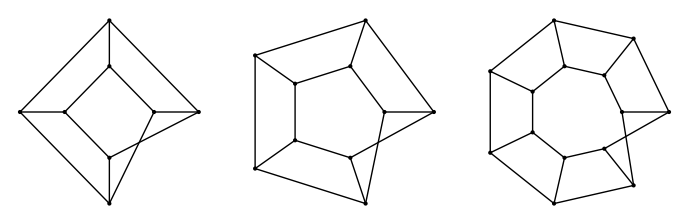

```mathematica
GraphicsRow[{lestev[4],lestev[5],lestev[7]}]
```